```mathematica
yk'[x_,y_]:=x+y
```

```mathematica
Clear["Global`*"]
```

```mathematica
s1={};
s2={};
h=0.1;
yp1=1;
yp2=1;
xp=0;
For[i=1,i≤ 10,i++,
yn1=yp1+h yk'[i h,yp1];
un=yp2+h yk'[i h,yp2];
yn2=yp2+1/2 h(yk'[i h,yp2]+yk'[i h,un]);
AppendTo[s1,{i h,yn1}];
AppendTo[s2,{i h,yn2}];
yp1=yn1;
yp2=yn2;]
Transpose@s1 //TableForm
Transpose@s2//TableForm
Transpose@Table[{s1[[i,1]],yy[s1[[i,1]]]},{i,1,Length[s1]}]//TableForm
```

0.1 | 0.2 | 0.3 | 0.4 | 0.5 | 0.6 | 0.7 | 0.8 | 0.9 | 1.
1.11 | 1.241 | 1.3951 | 1.57461 | 1.78207 | 2.02028 | 2.29231 | 2.60154 | 2.95169 | 3.34686

0.1 | 0.2 | 0.3 | 0.4 | 0.5 | 0.6 | 0.7 | 0.8 | 0.9 | 1.
1.1155 | 1.25363 | 1.41676 | 1.60752 | 1.82881 | 2.08383 | 2.37613 | 2.70963 | 3.08864 | 3.51795

0.1 | 0.2 | 0.3 | 0.4 | 0.5 | 0.6 | 0.7 | 0.8 | 0.9 | 1.
1.11034 | 1.24281 | 1.39972 | 1.58365 | 1.79744 | 2.04424 | 2.32751 | 2.65108 | 3.01921 | 3.43656

```mathematica
DSolveValue[{y'[x]==x+y[x],y[0]==1},y[x],x]
```

```mathematica
yy[x_]:=-1+2 ⅇ^x-x
```

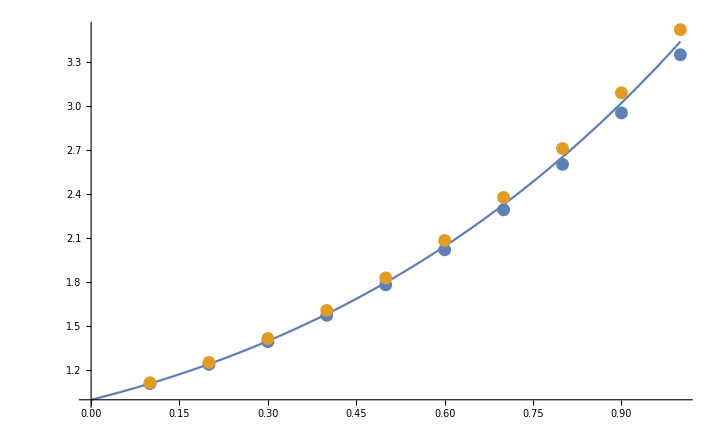

```mathematica
Show[Plot[-1+2 ⅇ^x-x,{x,0,1},PlotRange->All],ListPlot[{s1,s2}]]
```

```mathematica
Sum[(yy[s1[[i,1]]]-s1[[i,2]])^2,{i,1,Length[s1]}]
```

0.0172158

```mathematica
Sum[(yy[s2[[i,1]]]-s2[[i,2]])^2,{i,1,Length[s2]}]
```

0.0207921

```mathematica
Clear["Global`*"]
```

```mathematica
me[f_,y0_,x0_,h_]:=Module[{s={},yp=y0,yn,x,i},
For[i=0,i≤ 1/h,i++,
x=x0+i h;
un=yp+h f[x,yp];
yn=yp+h f[x,yp];
yp=yn;
AppendTo[s,{x,yn}];];
s]
```

```mathematica
yme[f_,y0_,x0_,h_]:=Module[{s={},yp=y0,un,yn,x,i},
For[i=0,i≤ 1/h,i++,
x=x0+i h;
un=yp+h f[x,yp];
yn=yp+1/2 h(f[x,yp]+f[x+h,un]);
yp=yn;
AppendTo[s,{x,yn}];];
s]
```

```mathematica
yme[#1+#2&,1,0,0.1]
```

{{0.,1.11},{0.1,1.24205},{0.2,1.39847},{0.3,1.5818},{0.4,1.79489},{0.5,2.04086},{0.6,2.32315},{0.7,2.64558},{0.8,3.01236},{0.9,3.42816},{1.,3.89812}}

```mathematica
me[#1+#2&,1,0,0.1]
```

{{0.,1.1},{0.1,1.22},{0.2,1.362},{0.3,1.5282},{0.4,1.72102},{0.5,1.94312},{0.6,2.19743},{0.7,2.48718},{0.8,2.8159},{0.9,3.18748},{1.,3.60623}}

```mathematica
s
```

{{0.05,1.05381},{0.1,1.11295},{0.15,1.17767},{0.2,1.24828},{0.25,1.32506},{0.3,1.40835},{0.35,1.49846},{0.4,1.59576},{0.45,1.70061},{0.5,1.81339},{0.55,1.93451},{0.6,2.0644},{0.65,2.20352},{0.7,2.35232},{0.75,2.51132},{0.8,2.68102},{0.85,2.86199},{0.9,3.05479},{0.95,3.26003},{1.,3.47836}}

```mathematica
Sum[(yy[s[[i,1]]]-s[[i,2]])^2,{i,1,Length[s]}]
```

0.00994593